# Numeric Integration Test

## Numeric Integration Rule One Dimensional

```mathematica
i = 2;
fun1D[x_,p_]:= 1.+x*Sin[p*p]+x*x*Sin[2*p*p]
For[p=0,p<13,p++,value=NIntegrate[fun1D[x,p],{x,-1.,1.},WorkingPrecision->16];Print[value]]
```

2.

2.606198284550454

2.659572164415588

1.499341835485549

2.36761778749446

1.825083430864047

2.169215575174691

1.617745418673051

2.480691807001154

1.347699766137747

1.417801801857337

1.935192061654517

1.429663752832786

```mathematica
fun1D[x_]:= 1.+x*Sin[p*p]+x*x*Sin[2*p*p]
```

```mathematica
fun3D[x_,y_,z_]:= 1.+x*Sin[p*p]+y*Sin[p]+z*Sin[1]+x*x*Sin[2*p*p]+y*y*Sin[2*p]+z*z*Sin[2]
```

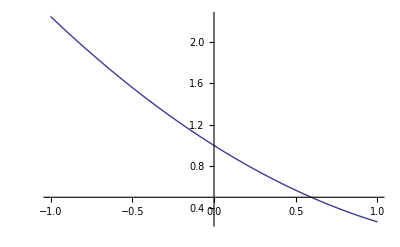

```mathematica
Plot[fun1D[x],{x,-1.,1.}]
```

```mathematica
NIntegrate[fun1D[x],{x,-1.,1.},WorkingPrecision->50]
```

NIntegrate::precw: The precision of the argument function (1.`  + x Sin[36] + x^2 Sin[72]) is less than WorkingPrecision (50.).

2.1692155751746908487126875090738376699063817829259

## Numeric Integration Rule Two Dimensional

```mathematica
i = 2;
p = 2;
fun2D[x_,y_]:= 1.+x*Sin[p*p]+y*Sin[p]+x*x*Sin[2*p*p]+y*y*Sin[2*p]
NIntegrate[fun2D[x,y],{x,-1.,1.},{y,-1.,1.}]
NIntegrate[fun2D[x,y],{x,0.,1.},{y,0.,1.-x}]
```

Quadrilateral parametric space

```mathematica
Plot3D[fun2D[x,y],{x,-1.,1.},{y,-1,1}]
```

-Graphics3D-

```mathematica
NIntegrate[fun2D[x,y],{x,-1.,1.},{y,-1.,1.},WorkingPrecision->30]
```

NIntegrate::precw: The precision of the argument function (1.`  + y Sin[6] + y^2 Sin[12] + x Sin[36] + x^2 Sin[72]) is less than WorkingPrecision (30.).

3.62300059301546840187154271382

Triangular parametric space

```mathematica
Plot3D[fun2D[x,y],{x,0.,1.},{y,0.,1.-x}]
```

-Graphics3D-

```mathematica
NIntegrate[fun2D[x,y],{x,0.,1.},{y,0.,1.-x},WorkingPrecision->30]
```

```mathematica
0.26457181178979317
```

## Numeric Integration Rule Three Dimensional

Cube parametric space

```mathematica
i = 2;
fun3D[x_,y_,z_,p_]:= 1.+x*Sin[p*p]+y*Sin[p]+z*Sin[1]+x*x*Sin[2*p*p]+y*y*Sin[2*p]+z*z*Sin[2];
For[p=0,p<13,p++,value=NIntegrate[fun3D[x,y,z,p],{x,-1.,1.},{y,-1.,1.},{z,-1.,1.},WorkingPrecision->16];Print[value]]
```

10.42479313820182

15.27437941460545

11.04494180837636

7.677052484946879

14.53355294584201

8.274403899286355

9.670794324232754

11.53739442808034

11.57981818843293

5.812959544695003

10.53052101423817

10.14195789337881

5.728572517515299

Tetrahedral parametric space

```mathematica
i = 2;
fun3D[x_,y_,z_,p_]:= 1.+x*Sin[p*p]+y*Sin[p]+z*Sin[1]+x*x*Sin[2*p*p]+y*y*Sin[2*p]+z*z*Sin[2];
For[p=0,p<13,p++,value=NIntegrate[fun3D[x,y,z,p],{x,0.,1.},{y,0.,1.-x},{z,0.,1-(x+y)},WorkingPrecision->16];Print[value]]
```

0.2168829139491411

0.3173154110219916

0.2271127993891759

0.2227611387537444

0.2227611387537444

0.1579731476556451

0.1592039908614216

0.2114714205797953

0.303659499822958

0.1789852244559073

0.1737775985061321

0.2150662368602839

0.1447150978897556

```mathematica
NIntegrate[fun3D[x,y,z,p],{x,0.,1.},{y,0.,1.-x},{z,0.,1-(x+y)},WorkingPrecision->50]
```

Pyramidal parametric space

```mathematica
NIntegrate[fun3D[x,y,z],{x,-1.,1.},{y,-1.,1.},{z,-1,1},WorkingPrecision->50]
```

Prism parametric space

```mathematica
i = 2;
fun3D[x_,y_,z_,p_]:= 1.+x*Sin[p*p]+y*Sin[p]+z*Sin[1]+x*x*Sin[2*p*p]+y*y*Sin[2*p]+z*z*Sin[2];
For[p=0,p<13,p++,value=NIntegrate[fun3D[x,y,z,p],{x,0.,1.},{y,0.,1.-x},{z,-1.,1.},WorkingPrecision->16];Print[value]]
```

1.303099142275227

2.167178941089052

1.392690078000387

1.315778182547335

1.211661359595075

0.804941139922707

0.8322427658548136

1.273714704879074

2.011749636188062

0.9422697063368188

0.9595782171944565

1.285030278864748

0.6670538495160184